### a)

```mathematica
Mq = {{sigma+1,3},{-2,sigma-1}};
Eigenvalues[Mq]
```

{-ⅈ √5+sigma,ⅈ √5+sigma}

### b)

```mathematica
systemsolver[x0_,y0_] := DSolve[{x'[t]==(sigma + 1)*x[t] + 3*y[t],
y'[t] == -2*x[t] + (sigma - 1)*y[t],x[0]==x0,y[0]==y0},
{x,y},{t}];
sol = systemsolver[u,v];
X[t_,x0_,y0_,sigma_] = {x[t],y[t]}/.sol
```

{{1/5 ⅇ^(sigma t) (5 u Cos[√5 t]+√5 u Sin[√5 t]+3 √5 v Sin[√5 t]),-1/5 ⅇ^(sigma t) (-5 v Cos[√5 t]+2 √5 u Sin[√5 t]+√5 v Sin[√5 t])}}

### c)

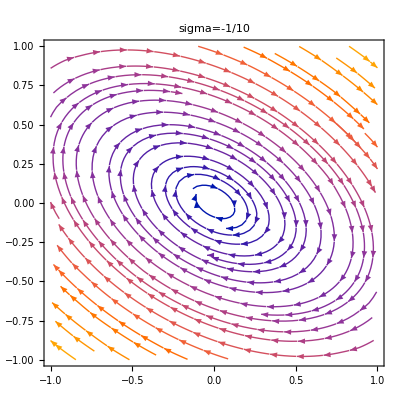

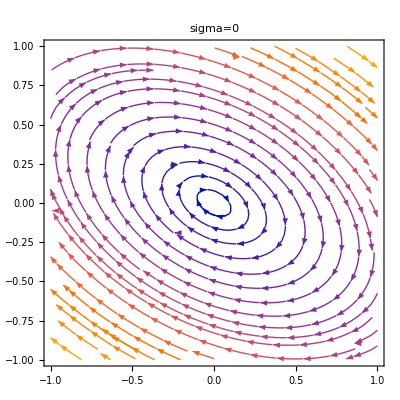

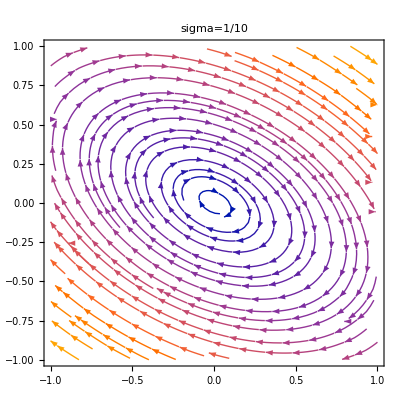

```mathematica
dotx[x_,y_,sigma_]:= (sigma + 1) * x + 3* y;
doty[x_,y_,sigma_]:= -2 * x + (sigma - 1) * y;
plot1 = StreamPlot[{dotx[x,y,-1/10],doty[x,y,-1/10]},{x,-1,1},{y,-1,1},PlotLabel->"sigma=-1/10"];

plot2 = StreamPlot[{dotx[x,y,0],doty[x,y,0]},{x,-1,1},{y,-1,1},PlotLabel->"sigma=0"]; 

plot3 =  StreamPlot[{dotx[x,y,1/10],doty[x,y,1/10]},{x,-1,1},{y,-1,1},PlotLabel->"sigma=1/10"];

Show[plot1]
Show[plot2]
Show[plot3]
```

#### d)

```mathematica
(*Make the system again but in another way, good way to practice*)
```

```mathematica
X[t_] = {x[t],y[t]};
dynsystem = X'[t] == Mq.X[t];
sol = DSolve[dynsystem,{x,y},t];
Xdot[t_,sigma_] = {x[t],y[t]}/.sol/.{C[1]->u,C[2]->v};
Xdot[t_,sigma_] //Simplify
```

{{1/5 ⅇ^(sigma_ t_) (5 u Cos[√5 t_]+√5 (u+3 v) Sin[√5 t_]),1/5 ⅇ^(sigma_ t_) (5 v Cos[√5 t_]-√5 (2 u+v) Sin[√5 t_])}}

```mathematica
sol = Solve [Xdot[t,0] == Xdot[0,0],t];
T = t/.sol (*calculate the period of the ellipse*)
T = Simplify[T/.C[1]->1]
```

{ConditionalExpression[(2 π C[1])/(√5), C[1]∈ℤ]}

{(2 π)/(√5)}

#### e)

```mathematica
sol = Xdot[t,0];
a = FindMaximum[Norm[sol]/.{u->1,v->2},t][[1]];
b = FindMinimum[Norm[sol]/.{u->1,v->2},t][[1]];
ratio = a/b;(*Calculate the ratio for the minor and major axes of the ellipse*)
NumberForm[ratio,10]
```

1.618033989

#### d) Analytically calculate the direction of the major ellipse axis in the (x, y) plane. For definiteness, normalise the vector to one and choose the direction so that the first component is positive.

```mathematica
timemajoraxis =FindMaximum[Norm[sol]/.{u->1,v->2},t][[2]][[1]](*Calculate the time where the major axis is placed*)
```

t→0.727378

```mathematica
direction = sol/.{u->1,v->2,timemajoraxis}
```

{{3.07,-1.89737}}

```mathematica
Normalize[direction[[1]]](*Normalizing the direction which is the answer*)
```

{0.850651,-0.525731}